# BinomialCoefficients 1.13

## documentation notebook

Eric Rowland
https://ericrowland.github.io/packages.html

## Introduction

BinomialCoefficients is a package containing implementations of several theorems on the residues and divisibility properties of binomial coefficients.
This introduction gets you started with a few features of the package; the next section provides a complete list of package symbols along with their usage messages and further examples.
The last section lists the theorems used by each symbol.

To use BinomialCoefficients, first you will need to load the package by evaluating the following cell.  (If you need help, see loading a package.)

```mathematica
<<BinomialCoefficients`
```

### Arithmetic properties of binomial coefficients

When every entry of Pascal's triangle is reduced modulo a prime or prime power, a nested structure is produced.  For example, reducing modulo 2 produces the familiar Sierpiński sieve:

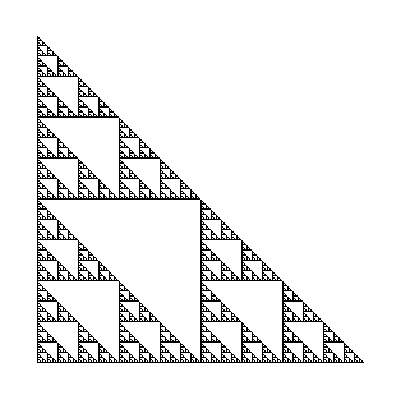
0.241168
-Graphics-

```mathematica
Column[Timing[ArrayPlot[Table[Mod[Binomial[n,m],2],{n,0,255},{m,0,n}]]]]
```

The symbols in this package compute various properties of these structures.

BinomialMod reduces a binomial coefficient modulo k using an indirect method.

```mathematica
Mod[Binomial[10,5],20]
```

12

```mathematica
BinomialMod[10,5,20]
```

12

For small numbers this is generally slower than the direct method, but for numbers of a suitable size the indirect method is faster.

```mathematica
Column[Timing[ArrayPlot[Table[BinomialMod[n,m,2],{n,0,255},{m,0,n}]]]]
```

0.88458
-Graphics-

In some cases there are faster ways than using the direct method:

```mathematica
Column[Timing[ArrayPlot[Table[Boole[BitAnd[BitNot[n],m]==0],{n,0,255},{m,0,n}]]]]
```

0.238719
-Graphics-

The symbol BinomialExponent corresponds to computing IntegerExponent of a Binomial.

```mathematica
IntegerExponent[Binomial[10,5],2]
```

2

```mathematica
BinomialExponent[10,5,2]
```

2

BinomialResidueCount counts the binomial coefficients on the nth row of Pascal's triangle that have a certain remainder when divided by k.
For example, this is the number of binomial coefficients on row 20 that are of the form 3i+1:

```mathematica
BinomialResidueCount[20,3,1]
```

5

Here is the 20th row modulo 3:

```mathematica
Mod[Binomial[20,Range[0,20]],3]
```

{1,2,1,0,0,0,0,0,0,2,1,2,0,0,0,0,0,0,1,2,1}

BinomialResidueCount also counts binomial coefficients on the nth row that are not divisible by k:

```mathematica
BinomialResidueCount[20,3]
```

9

It can also give answers for symbolic n in terms of the number of occurrences of various subwords in the base-p representation of n:
(The symbol DigitsCount belongs to my IntegerSequences package.)

```mathematica
BinomialResidueCount[n,3]
```

2^(IntegerSequences`DigitsCount[n,3,1]) 3^(IntegerSequences`DigitsCount[n,3,2])

## Package symbols

#### BinomialComplementMod

```mathematica
?BinomialComplementMod
```

RowBox[List["BinomialComplementMod", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["p", "TI"]]], "]"]] gives the residue of RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] modulo StyleBox["p", "TI"] after dividing by the largest power of StyleBox["p", "TI"] that divides RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]].
RowBox[List["BinomialComplementMod", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"], ",", SuperscriptBox[StyleBox["p", "TI"], "\"\[Alpha]\""]]], "]"]] gives the residue of RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] modulo SuperscriptBox[StyleBox["p", "TI"], "\"\[Alpha]\""] after dividing by the largest power of StyleBox["p", "TI"] that divides RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]].

```mathematica
Mod[Binomial[1000,373]/7^IntegerExponent[Binomial[1000,373],7],49]
```

41

```mathematica
BinomialComplementMod[1000,373,49]
```

41

#### BinomialExponent

```mathematica
?BinomialExponent
```

RowBox[List["BinomialExponent", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["k", "TI"]]], "]"]] gives the exponent of the highest power of StyleBox["k", "TI"] that divides RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]].

```mathematica
IntegerExponent[Binomial[1000,373],2]
```

6

```mathematica
BinomialExponent[1000,373,2]
```

6

```mathematica
Function[k,And@@Flatten[Table[BinomialExponent[n,m,k]==IntegerExponent[Binomial[n,m],k],{n,0,20},{m,0,20}]]]/@Range[2,5]
```

{True,True,True,True}

Kummer’s theorem says that the exponent of p dividing Binomial[n,m] is the number of carries involved in adding m and n-m in base p.

```mathematica
With[{p=3},And@@Flatten[Table[BinomialExponent[n,m,p]==Carries[m,n-m,p],{n,0,20},{m,0,n}]]]
```

True

However, for speed, BinomialExponent uses Legendre’s formula rather than explicitly counting carries:

```mathematica
AbsoluteTiming[Table[Carries[m,n-m,p],{p,Prime[Range[10]]},{n,0,100},{m,0,n}];]
```

{1.70058,Null}

```mathematica
AbsoluteTiming[Table[BinomialExponent[n,m,p],{p,Prime[Range[10]]},{n,0,100},{m,0,n}];]
```

{0.563362,Null}

#### BinomialMod

```mathematica
?BinomialMod
```

RowBox[List["BinomialMod", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"], ",", StyleBox["k", "TI"]]], "]"]] gives the residue of RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] modulo StyleBox["k", "TI"].

```mathematica
Mod[Binomial[1000,729],19]
```

13

```mathematica
BinomialMod[1000,729,19]
```

13

#### BinomialResidueCount

```mathematica
?BinomialResidueCount
```

RowBox[List["BinomialResidueCount", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["k", "TI"], ",", StyleBox["r", "TI"]]], "]"]] gives the number of binomial coefficients RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] that are congruent to a nonzero residue StyleBox["r", "TI"] modulo StyleBox["k", "TI"].
RowBox[List["BinomialResidueCount", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["k", "TI"]]], "]"]] gives the number of binomial coefficients RowBox[List["Binomial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["m", "TI"]]], "]"]] that are not divisible by StyleBox["k", "TI"].

Count the entries on the billionth row of Pascal's triangle in each nonzero residue class modulo 7:

```mathematica
BinomialResidueCount[10^9,7,Range[6]]
```

{87808,88000,88000,87616,87616,87808}

Compute the number of entries on the billionth row of Pascal's triangle that are not divisible by 7:

```mathematica
BinomialResidueCount[10^9,7]
```

526848

Compute a formula for the number of nonzero entries on row n of Pascal's triangle modulo 8 for symbolic n:

```mathematica
BinomialResidueCount[n,8]
```

2^(IntegerSequences`DigitsCount[n,2,1]) (1+3/8 IntegerSequences`DigitsCount[n,2,{0,1}]+1/8 (IntegerSequences`DigitsCount[n,2,{0,1}])^2+IntegerSequences`DigitsCount[n,2,{0,0,1}]+1/4 IntegerSequences`DigitsCount[n,2,{0,1,1}])

#### Carries

```mathematica
?Carries
```

RowBox[List["Carries", "[", RowBox[List[StyleBox["m", "TI"], ",", StyleBox["r", "TI"], ",", StyleBox["b", "TI"]]], "]"]] gives the number of carries involved in adding StyleBox["m", "TI"] and StyleBox["r", "TI"] in base StyleBox["b", "TI"].
RowBox[List["Carries", "[", RowBox[List[StyleBox["m", "TI"], ",", StyleBox["r", "TI"], ",", StyleBox["b", "TI"], ",", StyleBox["j", "TI"]]], "]"]] gives the number of carries onto or beyond the SuperscriptBox[StyleBox["b", "TI"], StyleBox["j", "TI"]] place.

```mathematica
Carries[999,1,10]
```

3

```mathematica
Carries[999,1,10,1]
```

2

#### CoprimeFactorial

```mathematica
?CoprimeFactorial
```

RowBox[List["CoprimeFactorial", "[", RowBox[List[StyleBox["n", "TI"], ",", StyleBox["p", "TI"]]], "]"]] computes the product of all natural numbers less than or equal to StyleBox["n", "TI"] that are not divisible by a prime StyleBox["p", "TI"].

```mathematica
Times@@Range[1,32,2]
```

191898783962510625

```mathematica
CoprimeFactorial[32,2]
```

191898783962510625

```mathematica
CoprimeFactorial[Range[10],5]
```

{1,2,6,24,24,144,1008,8064,72576,72576}

## Implementation details

BinomialComplementMod[n,m,p] uses Anton's theorem.
BinomialComplementMod[n,m,p^α] uses Granville's theorem.

BinomialExponent[n,m,p] uses Legendre’s formula.

BinomialMod[n,m,p] uses Lucas' theorem.
BinomialMod[n,m,p^α] uses Granville's generalization of Lucas' theorem.
When k is not a prime power, BinomialMod[n,m,k] uses Granville's theorem for each prime power factor of k and reconstructs the residue using the Chinese remainder theorem.

BinomialResidueCount[n,p,r] uses a theorem of Garfield and Wilf.
BinomialResidueCount[n,p^α] uses Rowland's generalization of Fine's theorem.
In other cases, BinomialResidueCount[n,k,r] and BinomialResidueCount[n,k] use BinomialMod to explicitly tally residues.